```mathematica
Clculation of M_core and Sigma Matrix in the presence of Space- Charge
Author : N. S. MIRIAN
M_core Matrix
```

-Charge+  and Clculation in Matrix of^2 presence Sigma the M_core

## 1- M_CORE ------> Eq.(24)

```mathematica
(1)  X   is eigen vectror Eq (21)
```

```mathematica
i=Sqrt[-1];
```

```mathematica
x=({{i*ωh*(8*ΔKx*(KK^3)+4*(KK^2)*k^2+ΔKy*(k^4))/(2*KK^2*k^3),-i*ωh*(8*ΔKx*(KK^3)+4*(KK^2)*k^2+ΔKy*(k^4))/(2*KK^2*k^3),(2*ΔKx)/k+((ΔKy*k)/4+(KK*k*(2*ΔKx+2))/4)/KK^2,(2*ΔKx)/k+((ΔKy*k)/4+(KK*k*(2*ΔKx+2))/4)/KK^2},{2*KK*(k^2-2*ΔKx*KK)/k^3,2*KK*(k^2-2*ΔKx*KK)/k^3,-(2*ΔKx*i*ωl)/k,(2*ΔKx*i*ωl)/k},{(4*KK^2*k^2-4*ΔKy*KK*k^2+(ΔKy*k^4)-(8*ΔKx*KK^3))/((2*KK*k)^2),(4*KK^2*k^2-4*ΔKy*KK*k^2+(ΔKy*k^4)-(8*ΔKx*KK^3))/((2*KK*k)^2),-i*ωl*(2*KK-ΔKy+2*ΔKx*KK)/(2*KK^2),i*ωl*(2*KK-ΔKy+2*ΔKx*KK)/(2*KK^2)},{(ΔKy*(i*ωh))/KK,(ΔKy*(-i*ωh))/KK,ΔKy/(2*KK)+1,ΔKy/(2*KK)+1}});

x2=Inverse[({{i*ωh*(8*ΔKx*(KK^3)+4*(KK^2)*k^2+ΔKy*(k^4))/(2*KK^2*k^3),-i*ωh*(8*ΔKx*(KK^3)+4*(KK^2)*k^2+ΔKy*(k^4))/(2*KK^2*k^3),(2*ΔKx)/k+((ΔKy*k)/4+(KK*k*(2*ΔKx+2))/4)/KK^2,(2*ΔKx)/k+((ΔKy*k)/4+(KK*k*(2*ΔKx+2))/4)/KK^2},{2*KK*(k^2-2*ΔKx*KK)/k^3,2*KK*(k^2-2*ΔKx*KK)/k^3,-(2*ΔKx*i*ωl)/k,(2*ΔKx*i*ωl)/k},{(4*KK^2*k^2-4*ΔKy*KK*k^2+(ΔKy*k^4)-(8*ΔKx*KK^3))/((2*KK*k)^2),(4*KK^2*k^2-4*ΔKy*KK*k^2+(ΔKy*k^4)-(8*ΔKx*KK^3))/((2*KK*k)^2),-i*ωl*(2*KK-ΔKy+2*ΔKx*KK)/(2*KK^2),i*ωl*(2*KK-ΔKy+2*ΔKx*KK)/(2*KK^2)},{(ΔKy*(i*ωh))/KK,(ΔKy*(-i*ωh))/KK,ΔKy/(2*KK)+1,ΔKy/(2*KK)+1}})];
lambda=({{exp[i*s*ωh],0,0,0},{0,exp[-i*s*ωh],0,0},{0,0,exp[i*s*ωl],0},{0,0,0,exp[-i*s*ωl]}});
M=x.lambda.x2;

M=Expand[M];
M=M/.ΔKx^b_/;b≥2->0;
M=M/.ΔKy^b_/;b≥2->0;
M=M/.(ΔKx*ΔKy)->0;
M3=FullSimplify[M, {s∈Reals, ωh∈Reals , ωl∈Reals}];


MatrixForm[M3]
(*M4={M3, ΔKx= ΔKy=Δk}*)
```

(((4 KK^2+k^2 ΔKy) exp[-ⅈ s ωh]+(4 KK^2+k^2 ΔKy) exp[ⅈ s ωh]-k^2 ΔKy (exp[-ⅈ s ωl]+exp[ⅈ s ωl]))/(8 KK^2) | (ⅈ (4 KK^2 (4 KK ΔKx+k^2 (1+ΔKx))+k^4 ΔKy) (4 ωh ωl (-exp[-ⅈ s ωh]+exp[ⅈ s ωh])+k^2 (exp[-ⅈ s ωl]-exp[ⅈ s ωl])))/(32 k^2 KK^3 ωl) | -(ⅈ (-4 KK ΔKx ωh ωl exp[-ⅈ s ωh]+4 KK ΔKx ωh ωl exp[ⅈ s ωh]+(4 KK^2 ΔKx+k^2 (KK+KK ΔKx+ΔKy)) (exp[-ⅈ s ωl]-exp[ⅈ s ωl])))/(4 k KK ωl) | -((4 KK^2 (4 KK ΔKx+k^2 (1+ΔKx))+k^4 ΔKy) (exp[-ⅈ s ωh]+exp[ⅈ s ωh]-exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(16 k KK^3)
(ⅈ KK (k^2-4 KK ΔKx) (exp[-ⅈ s ωh]-exp[ⅈ s ωh]))/(2 k^2 ωh) | 1/2 ((1+ΔKx) exp[-ⅈ s ωh]+(1+ΔKx) exp[ⅈ s ωh]-ΔKx (exp[-ⅈ s ωl]+exp[ⅈ s ωl])) | (KK ΔKx (-exp[-ⅈ s ωh]-exp[ⅈ s ωh]+exp[-ⅈ s ωl]+exp[ⅈ s ωl]))/k | -(ⅈ (k^2 (1+ΔKx) exp[-ⅈ s ωh]-k^2 (1+ΔKx) exp[ⅈ s ωh]+4 ΔKx ωh ωl (-exp[-ⅈ s ωl]+exp[ⅈ s ωl])))/(4 k ωh)
(ⅈ ((-16 KK^3 ΔKx+4 k^2 KK (KK-ΔKy)+k^4 ΔKy) exp[-ⅈ s ωh]+(16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (-KK+ΔKy)) exp[ⅈ s ωh]+4 k^2 ΔKy ωh ωl (-exp[-ⅈ s ωl]+exp[ⅈ s ωl])))/(16 k KK^2 ωh) | (k (4 KK (KK+KK ΔKx-ΔKy)+k^2 ΔKy) (exp[-ⅈ s ωh]+exp[ⅈ s ωh]-exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(16 KK^3) | 1/2 (-ΔKx exp[-ⅈ s ωh]-ΔKx exp[ⅈ s ωh]+(1+ΔKx) (exp[-ⅈ s ωl]+exp[ⅈ s ωl])) | -(ⅈ (4 KK (KK+KK ΔKx-ΔKy)+k^2 ΔKy) (k^2 (exp[-ⅈ s ωh]-exp[ⅈ s ωh])+4 ωh ωl (-exp[-ⅈ s ωl]+exp[ⅈ s ωl])))/(32 KK^3 ωh)
(k ΔKy (exp[-ⅈ s ωh]+exp[ⅈ s ωh]-exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(4 KK) | (ⅈ k (-4 ΔKy ωh ωl exp[-ⅈ s ωh]+4 ΔKy ωh ωl exp[ⅈ s ωh]+(4 KK^2+k^2 ΔKy) (exp[-ⅈ s ωl]-exp[ⅈ s ωl])))/(16 KK^2 ωl) | -(ⅈ (KK+ΔKy) (exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(2 ωl) | -(k^2 ΔKy exp[-ⅈ s ωh]+k^2 ΔKy exp[ⅈ s ωh]-(4 KK^2+k^2 ΔKy) (exp[-ⅈ s ωl]+exp[ⅈ s ωl]))/(8 KK^2))

M3 is new M_core
Test 1
M_core TEST

```mathematica
Mcore=MatrixForm[FullSimplify[ReplaceAll[M3,{ΔKx->0, ΔKy->0}],{ωh ∈Reals, ωl∈Reals, s∈Reals}]]
```

(1/2 (exp[-ⅈ s ωh]+exp[ⅈ s ωh]) | (ⅈ (4 ωh ωl (-exp[-ⅈ s ωh]+exp[ⅈ s ωh])+k^2 (exp[-ⅈ s ωl]-exp[ⅈ s ωl])))/(8 KK ωl) | -(ⅈ k (exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(4 ωl) | (k (-exp[-ⅈ s ωh]-exp[ⅈ s ωh]+exp[-ⅈ s ωl]+exp[ⅈ s ωl]))/(4 KK)
(ⅈ KK (exp[-ⅈ s ωh]-exp[ⅈ s ωh]))/(2 ωh) | 1/2 (exp[-ⅈ s ωh]+exp[ⅈ s ωh]) | 0 | -(ⅈ k (exp[-ⅈ s ωh]-exp[ⅈ s ωh]))/(4 ωh)
(ⅈ k (exp[-ⅈ s ωh]-exp[ⅈ s ωh]))/(4 ωh) | (k (exp[-ⅈ s ωh]+exp[ⅈ s ωh]-exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(4 KK) | 1/2 (exp[-ⅈ s ωl]+exp[ⅈ s ωl]) | (ⅈ (k^2 (-exp[-ⅈ s ωh]+exp[ⅈ s ωh])+4 ωh ωl (exp[-ⅈ s ωl]-exp[ⅈ s ωl])))/(8 KK ωh)
0 | (ⅈ k (exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(4 ωl) | -(ⅈ KK (exp[-ⅈ s ωl]-exp[ⅈ s ωl]))/(2 ωl) | 1/2 (exp[-ⅈ s ωl]+exp[ⅈ s ωl]))

good agreement with Eq.24

## 2- Sigma Matrix ----------> Eq. (36)

```mathematica
xc=({{-i*ωh*(8*ΔKx*(KK^3)+4*(KK^2)*k^2+ΔKy*(k^4))/(2*KK^2*k^3), 2*KK*(k^2-2*ΔKx*KK)/k^3, (4*KK^2*k^2-4*ΔKy*KK*k^2+(ΔKy*k^4)-(8*ΔKx*KK^3))/((2*KK*k)^2), ΔKy*(-i*ωh)/KK}, {i*ωh*(8*ΔKx*(KK^3)+4*(KK^2)*k^2+ΔKy*(k^4))/(2*KK^2*k^3), 2*KK*(k^2-2*ΔKx*KK)/k^3, (4*KK^2*k^2-4*ΔKy*KK*k^2+(ΔKy*k^4)-(8*ΔKx*KK^3))/((2*KK*k)^2), ΔKy*(i*ωh)/KK}, {(2*ΔKx)/k+((ΔKy*k)/4+(KK*k*(2*ΔKx+2))/4)/KK^2, (2*ΔKx*i*ωl)/k, i*ωl*(2*KK-ΔKy+2*ΔKx*KK)/(2*KK^2), ΔKy/(2*KK)+1}, {(2*ΔKx)/k+((ΔKy*k)/4+(KK*k*(2*ΔKx+2))/4)/KK^2, -(2*ΔKx*i*ωl)/k, -i*ωl*(2*KK-ΔKy+2*ΔKx*KK)/(2*KK^2), ΔKy/(2*KK)+1}});


S={{2*Ah^2,0,0,0},{0,2*Ah^2,0,0},{0,0,2*Al^2,0},{0,0,0,2*Al^2}};
SS=x.S.xc;



R=({{Cos[k*s/2],0,Sin[k*s/2],0},{0,Cos[k*s/2],0,Sin[k*s/2]},{-Sin[k*s/2],0,Cos[k*s/2],0},{0,-Sin[k*s/2],0,Cos[k*s/2]}});


RN=({{Cos[k*s/2],0,-Sin[k*s/2],0},{0,Cos[k*s/2],0,-Sin[k*s/2]},{Sin[k*s/2],0,Cos[k*s/2],0},{0,Sin[k*s/2],0,Cos[k*s/2]}});




Sigma1=R.SS.RN;
Sigma110=Expand[Sigma1];
Sigma110=Sigma110/.ΔKy^b_/;b≥2->0;
Sigma110=Sigma110/.ΔKx^b_/;b≥2->0;
Sigma110=Sigma110/.(ΔKy*ΔKx)->0;
Sigma110=FullSimplify[Sigma110];
MatrixForm[Sigma110]
```

(((Al^2 k^4 (8 KK^2 ΔKx+k^2 (KK+2 KK ΔKx+ΔKy))+8 Ah^2 KK (2 KK^2 (k^2+4 KK ΔKx)+k^4 ΔKy) ωh^2) Cos[(k s)/2]^2-k^2 (Ah^2 KK (-8 KK^3 ΔKx+2 k^2 KK (KK-2 ΔKy)+k^4 ΔKy)+2 Al^2 k^2 (KK+2 KK ΔKx-ΔKy) ωl^2) (-1+Cos[k s]))/(k^4 KK^3) | ((Ah^2 KK (-16 KK^3 ΔKx+k^4 ΔKy+4 k^2 (KK^2-KK ΔKy+ΔKy ωh^2))+Al^2 k^2 (k^2 (KK+KK ΔKx+ΔKy)+4 KK ΔKx (KK+ωl^2))) Sin[k s])/(k^3 KK^2) | -((2 Ah^2 KK (-k^6 ΔKy+32 KK^3 ΔKx ωh^2+8 k^2 KK^2 (KK ΔKx+ωh^2)+k^4 (-2 KK^2+4 KK ΔKy+4 ΔKy ωh^2))+Al^2 k^4 (8 KK^2 ΔKx+k^2 (KK+2 KK ΔKx+ΔKy)-4 (KK+2 KK ΔKx-ΔKy) ωl^2)) Sin[k s])/(2 k^4 KK^3) | (KK (Ah^2 (-16 KK^3 ΔKx+4 k^2 KK (KK-ΔKy)+k^4 ΔKy)+4 Al^2 k^2 ΔKx ωl^2) (-1+Cos[k s])+k^2 (Al^2 (4 KK^2 ΔKx+k^2 (KK+KK ΔKx+ΔKy))+4 Ah^2 KK ΔKy ωh^2) (1+Cos[k s]))/(k^3 KK^2)
((Ah^2 KK (-16 KK^3 ΔKx+k^4 ΔKy+4 k^2 (KK^2-KK ΔKy+ΔKy ωh^2))+Al^2 k^2 (k^2 (KK+KK ΔKx+ΔKy)+4 KK ΔKx (KK+ωl^2))) Sin[k s])/(k^3 KK^2) | (-2 Al^2 k^4 (KK+ΔKy) (-1+Cos[k s])+8 Ah^2 KK^3 (k^2-4 KK ΔKx) (1+Cos[k s]))/(k^4 KK) | (k^2 (Al^2 (4 KK^2 ΔKx+k^2 (KK+KK ΔKx+ΔKy))+4 Ah^2 KK ΔKy ωh^2) (-1+Cos[k s])+KK (Ah^2 (-16 KK^3 ΔKx+4 k^2 KK (KK-ΔKy)+k^4 ΔKy)+4 Al^2 k^2 ΔKx ωl^2) (1+Cos[k s]))/(k^3 KK^2) | (2 (4 Ah^2 KK^3 (-k^2+4 KK ΔKx)+Al^2 k^4 (KK+ΔKy)) Sin[k s])/(k^4 KK)
-((2 Ah^2 KK (-k^6 ΔKy+32 KK^3 ΔKx ωh^2+8 k^2 KK^2 (KK ΔKx+ωh^2)+k^4 (-2 KK^2+4 KK ΔKy+4 ΔKy ωh^2))+Al^2 k^4 (8 KK^2 ΔKx+k^2 (KK+2 KK ΔKx+ΔKy)-4 (KK+2 KK ΔKx-ΔKy) ωl^2)) Sin[k s])/(2 k^4 KK^3) | (k^2 (Al^2 (4 KK^2 ΔKx+k^2 (KK+KK ΔKx+ΔKy))+4 Ah^2 KK ΔKy ωh^2) (-1+Cos[k s])+KK (Ah^2 (-16 KK^3 ΔKx+4 k^2 KK (KK-ΔKy)+k^4 ΔKy)+4 Al^2 k^2 ΔKx ωl^2) (1+Cos[k s]))/(k^3 KK^2) | (k^2 (Ah^2 KK (-8 KK^3 ΔKx+2 k^2 KK (KK-2 ΔKy)+k^4 ΔKy)+2 Al^2 k^2 (KK+2 KK ΔKx-ΔKy) ωl^2) (1+Cos[k s])+(Al^2 (8 k^4 KK^2 ΔKx+k^6 (KK+2 KK ΔKx+ΔKy))+8 Ah^2 KK (2 KK^2 (k^2+4 KK ΔKx)+k^4 ΔKy) ωh^2) Sin[(k s)/2]^2)/(k^4 KK^3) | -((Ah^2 KK (-16 KK^3 ΔKx+k^4 ΔKy+4 k^2 (KK^2-KK ΔKy+ΔKy ωh^2))+Al^2 k^2 (k^2 (KK+KK ΔKx+ΔKy)+4 KK ΔKx (KK+ωl^2))) Sin[k s])/(k^3 KK^2)
(KK (Ah^2 (-16 KK^3 ΔKx+4 k^2 KK (KK-ΔKy)+k^4 ΔKy)+4 Al^2 k^2 ΔKx ωl^2) (-1+Cos[k s])+k^2 (Al^2 (4 KK^2 ΔKx+k^2 (KK+KK ΔKx+ΔKy))+4 Ah^2 KK ΔKy ωh^2) (1+Cos[k s]))/(k^3 KK^2) | (2 (4 Ah^2 KK^3 (-k^2+4 KK ΔKx)+Al^2 k^4 (KK+ΔKy)) Sin[k s])/(k^4 KK) | -((Ah^2 KK (-16 KK^3 ΔKx+k^4 ΔKy+4 k^2 (KK^2-KK ΔKy+ΔKy ωh^2))+Al^2 k^2 (k^2 (KK+KK ΔKx+ΔKy)+4 KK ΔKx (KK+ωl^2))) Sin[k s])/(k^3 KK^2) | (-8 Ah^2 KK^3 (k^2-4 KK ΔKx) (-1+Cos[k s])+2 Al^2 k^4 (KK+ΔKy) (1+Cos[k s]))/(k^4 KK))

Test 2
SS Test according to Eq.36

```mathematica
SS1=Expand[SS];
SS1=SS1/.ΔKy^b_/;b≥2->0;
SS1=SS1/.ΔKx^b_/;b≥2->0;
SS1=SS1/.(ΔKy*ΔKx)->0;
SS=FullSimplify[SS1];
MatrixForm[SS]
```

((Al^2 (8 k^4 KK^2 ΔKx+k^6 (KK+2 KK ΔKx+ΔKy))+8 Ah^2 KK (2 KK^2 (k^2+4 KK ΔKx)+k^4 ΔKy) ωh^2)/(k^4 KK^3) | 0 | 0 | (2 (Al^2 (4 KK^2 ΔKx+k^2 (KK+KK ΔKx+ΔKy))+4 Ah^2 KK ΔKy ωh^2))/(k KK^2)
0 | (16 Ah^2 KK^2 (k^2-4 KK ΔKx))/k^4 | (2 Ah^2 (-16 KK^3 ΔKx+4 k^2 KK (KK-ΔKy)+k^4 ΔKy)+8 Al^2 k^2 ΔKx ωl^2)/(k^3 KK) | 0
0 | (2 Ah^2 (-16 KK^3 ΔKx+4 k^2 KK (KK-ΔKy)+k^4 ΔKy)+8 Al^2 k^2 ΔKx ωl^2)/(k^3 KK) | (2 (Ah^2 KK (-8 KK^3 ΔKx+2 k^2 KK (KK-2 ΔKy)+k^4 ΔKy)+2 Al^2 k^2 (KK+2 KK ΔKx-ΔKy) ωl^2))/(k^2 KK^3) | 0
(2 (Al^2 (4 KK^2 ΔKx+k^2 (KK+KK ΔKx+ΔKy))+4 Ah^2 KK ΔKy ωh^2))/(k KK^2) | 0 | 0 | (4 Al^2 (KK+ΔKy))/KK)

```mathematica
SS3=ReplaceAll[SS, {ΔKx-> 0,ΔKy->0}];
SS3=FullSimplify[SS3];
MatrixForm[SS3]
```

((Al^2 k^2)/KK^2+(16 Ah^2 ωh^2)/k^2 | 0 | 0 | (2 Al^2 k)/KK
0 | (16 Ah^2 KK^2)/k^2 | (8 Ah^2 KK)/k | 0
0 | (8 Ah^2 KK)/k | 4 (Ah^2+(Al^2 ωl^2)/KK^2) | 0
(2 Al^2 k)/KK | 0 | 0 | 4 Al^2)

good agreement !

## 3- Sigma Matrix ----------------> Eq. (36)

```mathematica
sx=({{Sigma110[[1,1]], Sigma110[[1,2]]}, {Sigma110[[2,1]], Sigma110[[2,2]]}});
Ex=Sqrt[Det[sx]];
```

```mathematica
EX=Expand[Ex];
Ex2=EX/.ΔKx^b_/;b≥2->0;
Ex2=Ex2/.ΔKy^b_/;b≥2->0;
Ex2=Ex2/.(ΔKy*ΔKx)->0;

Ex2=FullSimplify[Ex2];
Ex=Sqrt[Ex2];
Ex=FullSimplify[Ex]
```

2^(1/4) (1/(k^4 KK^2)(16 Ah^4 KK^2 (3 KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (3+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (ωh-ωl) (ωh+ωl)+4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))+2 (Ah^2 Al^2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))+16 Ah^4 KK^2 (2 KK^2+k^2 ΔKy) ωh^2-2 Al^4 k^4 (1+2 ΔKx) ωl^2) Cos[k s]+(16 Ah^4 KK^2 (KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (1+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (-ωh^2+ωl^2)-4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))) Cos[2 k s]))^(1/4)

Ex is the emittance in x direction

```mathematica
sy=({{Sigma110[[3,3]],Sigma110[[3,4]]},{Sigma110[[4,3]],Sigma110[[4,4]]}});
Ey=Sqrt[Det[{{Sigma110[[3,3]],Sigma110[[3,4]]},{Sigma110[[4,3]],Sigma110[[4,4]]}}]];


Ey2=Ey/.ΔKx^b_/;b≥2->0;
Ey2=Ey2/.ΔKy^b_/;b≥2->0;
Ey2=Ey2/.(ΔKx*ΔKy)->0;
Ey2=FullSimplify[Ey2];

Ey=Sqrt[Ey2];
Ey=Simplify[Ey]
```

2^(1/4) (1/(k^4 KK^2)(16 Ah^4 KK^2 (3 KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (3+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (ωh-ωl) (ωh+ωl)+4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))-2 (Ah^2 Al^2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))+16 Ah^4 KK^2 (2 KK^2+k^2 ΔKy) ωh^2-2 Al^4 k^4 (1+2 ΔKx) ωl^2) Cos[k s]+(16 Ah^4 KK^2 (KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (1+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (-ωh^2+ωl^2)-4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))) Cos[2 k s]))^(1/4)

Ey is the emittance in y direction
Test 3 
without SC

```mathematica
ex0=ReplaceAll[Ex, {ΔKx-> 0,ΔKy->0}]
ey0=ReplaceAll[Ey, {ΔKx-> 0,ΔKy->0}]
```

2^(1/4) ((48 Ah^4 KK^4 ωh^2+3 Al^4 k^4 ωl^2+Ah^2 Al^2 (4 k^4 KK^2+4 k^2 KK (KK ωh^2+KK ωl^2))+2 (32 Ah^4 KK^4 ωh^2-2 Al^4 k^4 ωl^2) Cos[k s]+(16 Ah^4 KK^4 ωh^2+Al^4 k^4 ωl^2+Ah^2 Al^2 (4 k^4 KK^2-4 k^2 KK (KK ωh^2+KK ωl^2))) Cos[2 k s])/(k^4 KK^2))^(1/4)

2^(1/4) ((48 Ah^4 KK^4 ωh^2+3 Al^4 k^4 ωl^2+Ah^2 Al^2 (4 k^4 KK^2+4 k^2 KK (KK ωh^2+KK ωl^2))-2 (32 Ah^4 KK^4 ωh^2-2 Al^4 k^4 ωl^2) Cos[k s]+(16 Ah^4 KK^4 ωh^2+Al^4 k^4 ωl^2+Ah^2 Al^2 (4 k^4 KK^2-4 k^2 KK (KK ωh^2+KK ωl^2))) Cos[2 k s])/(k^4 KK^2))^(1/4)

```mathematica
ϵ=2*KK/k*((k^2 +4*KK)/(k^2- 4*KK))^(1/4);  (* Eq. 39 as a assumtion for ex0=ey0 *)

ex02=FullSimplify[ReplaceAll[ex0,{ωh->Sqrt[KK+k^2/4],ωl->Sqrt[k^2/4-KK],Al->ϵ*Ah}]]
ey02=FullSimplify[ReplaceAll[ey0,{ωh->Sqrt[KK+k^2/4],ωl->Sqrt[k^2/4-KK],Al->ϵ*Ah}]]
```

2 ((Ah^4 KK^2 (4 KK+k^2 (1+√((k^2+4 KK)/(k^2-4 KK)))) (3+Cos[2 k s]))/k^4)^(1/4)

2 ((Ah^4 KK^2 (4 KK+k^2 (1+√((k^2+4 KK)/(k^2-4 KK)))) (3+Cos[2 k s]))/k^4)^(1/4)

As can be ssen the emittances are equal but both of them are depended  on Cos[2ks ] !!!

((((2 π^2)/L^2+(4 (1+√3) π^2)/L^2) (3+Cos[(4 π s)/L]))^(1/4))/(√2)

((2 π^2+4 (1+√3) π^2)^(1/4) (3+Cos[4 π s])^(1/4))/(√2)

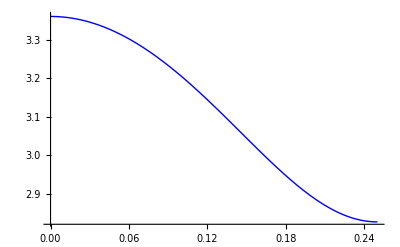

```mathematica
e01= ReplaceAll[ex02,{KK->k^2/8}];
e02= ReplaceAll[e01,{k->(2*π/L), Ah-> 1}]
e02= ReplaceAll[e02,{L-> 1}]
Plot[e02,{s,0,0.25},PlotStyle->Blue]
```

Test 4
Eq. (38) ℰ=√(det(σ))  = costant

```mathematica
t1=ReplaceAll[Sigma110, {ΔKx-> 0,ΔKy->0}];
Emitt=FullSimplify[Sqrt[Det[t1]]]
```

64 √((Ah^4 Al^4 ωh^2 ωl^2)/k^4)

It is constant !! True

## 4 - Examples

(1) Example -1
ex0 and ey0 are the emittance without space charge !
Plot emittance x and y
1-first example
k=2π/L,   KK=Mk,   Al=ϵAh, kk=k^2/8,   ΔKx=M*ΔKy,   
M=3, ϵ=Sqrt[1/16 Sqrt[3] k^2], L=5

```mathematica
Ex=FullSimplify[ReplaceAll[Ex,{ωh->Sqrt[KK+k^2/4],ωl->Sqrt[k^2/4-KK],Al->ϵ*Ah,ΔKx->M*ΔK,ΔKy->ΔK,k->(2*π/L)}],{Ah>0,ΔK>0,L>0}];
Ey=FullSimplify[ReplaceAll[Ex,{ωh->Sqrt[KK+k^2/4],ωl->Sqrt[k^2/4-KK],Al->ϵ*Ah,ΔKx->M*ΔK,ΔKy->ΔK, k->(2*π/L)}],{Ah>0,ΔK>0,L>0}];

Ex1=ReplaceAll[Ex,{KK->k^2/8,M->3,ΔK->0.1*k^2/8,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E1=ReplaceAll[Ex1,{Ah->1,L->1}];
P1=Plot[E1,{s,0,0.25},PlotStyle->Red,AxesLabel->{s,Subscript[ε,x]}];


Ex1=ReplaceAll[Ex,{KK->k^2/8,ΔK->0.0,M->3,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E1=ReplaceAll[Ex1,{Ah->1,L->1}];
P12=Plot[E1,{s,0,0.25},PlotStyle->{Red,Dashed},AxesLabel->{s,Subscript[ε,x]}];


Ey1=ReplaceAll[Ey,{KK->k^2/8,ΔK->0.1*k^2/8,M->.3,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E2=ReplaceAll[Ey1,{Ah->1,L->1}];
P2=Plot[E2,{s,0,0.25},PlotStyle->Blue,AxesLabel->{s,Subscript[ε,y] Subscript[ε,x]}];

Ey1=ReplaceAll[Ey,{KK->k^2/8,ΔK->0,M->.3,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E1=ReplaceAll[Ey1,{Ah->1,L->1}];
P21=Plot[E1,{s,0,0.25},PlotStyle->{Blue,Dashed},AxesLabel->{s,Subscript[ε,y]}];
Show[{P2,P21,P12,P1},PlotRange->{5,23}]
Export["emitance1.pdf",%]
```

(2 ) Example -2 
k = 2 π/L,   KK = Mk,   Al = ϵAh, kk = k^2/8,   ΔKx = M*ΔKy,   
M = 3, ϵ = Sqrt[1/16 Sqrt[3] k^2], L=5

```mathematica
Ex1=ReplaceAll[Ex,{KK->k^2/8,ΔK->0.1*k^2/8,M->3,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E1=ReplaceAll[Ex1,{Ah->1,L->5}]
P1=Plot[E1,{s,0,1.5},PlotStyle->Red,AxesLabel->{s,Subscript[ε,x]}];


Ex1=ReplaceAll[Ex,{KK->k^2/8,ΔK->0.0,M->3,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E1=ReplaceAll[Ex1,{Ah->1,L->5}]
P12=Plot[E1,{s,0,1.5},PlotStyle->{Red,Dashed},AxesLabel->{s,Subscript[ε,x]}];


Ey1=ReplaceAll[Ey,{KK->k^2/8,ΔK->0.1*k^2/82*π/L,M->3,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E2=ReplaceAll[Ey1,{Ah->1,L->5}]
P2=Plot[E2,{s,0,1.5},PlotStyle->Blue,AxesLabel->{s,Subscript[ε,y] Subscript[ε,x]}];

Ey1=ReplaceAll[Ey,{KK->k^2/8,ΔK->0.0,M->3,ϵ->Sqrt[1/16 Sqrt[3] k^2]}];
E2=ReplaceAll[Ey1,{Ah->1,L->5}]
P21=Plot[E2,{s,0,1.5},PlotStyle->{Blue,Dashed},AxesLabel->{s,Subscript[ε,y]}];


Show[{P2,P1,P12,P21},PlotRange->{1.2,2.8}]
Export["emitance2.pdf",%]
```

## 5- Beta function ------------> Eq.(40 )

```mathematica
βx=Sigma110[[1,1]]/Ex;
βy=Sigma110[[3,3]]/Ey;
Simplify[βx]
Simplify[βy]
```

((Al^2 k^4 (8 KK^2 ΔKx+k^2 (KK+2 KK ΔKx+ΔKy))+8 Ah^2 KK (2 KK^2 (k^2+4 KK ΔKx)+k^4 ΔKy) ωh^2) Cos[(k s)/2]^2-k^2 (Ah^2 KK (-8 KK^3 ΔKx+2 k^2 KK (KK-2 ΔKy)+k^4 ΔKy)+2 Al^2 k^2 (KK+2 KK ΔKx-ΔKy) ωl^2) (-1+Cos[k s]))/(√2 k^4 KK^3 √(1/(k^4 KK^2)(16 Ah^4 KK^2 (3 KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (3+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (ωh-ωl) (ωh+ωl)+4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))+2 (Ah^2 Al^2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))+16 Ah^4 KK^2 (2 KK^2+k^2 ΔKy) ωh^2-2 Al^4 k^4 (1+2 ΔKx) ωl^2) Cos[k s]+(16 Ah^4 KK^2 (KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (1+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (-ωh^2+ωl^2)-4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))) Cos[2 k s])))

(k^2 (Ah^2 KK (-8 KK^3 ΔKx+2 k^2 KK (KK-2 ΔKy)+k^4 ΔKy)+2 Al^2 k^2 (KK+2 KK ΔKx-ΔKy) ωl^2) (1+Cos[k s])+(Al^2 (8 k^4 KK^2 ΔKx+k^6 (KK+2 KK ΔKx+ΔKy))+8 Ah^2 KK (2 KK^2 (k^2+4 KK ΔKx)+k^4 ΔKy) ωh^2) Sin[(k s)/2]^2)/(√2 k^4 KK^3 √(1/(k^4 KK^2)(16 Ah^4 KK^2 (3 KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (3+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (ωh-ωl) (ωh+ωl)+4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))-2 (Ah^2 Al^2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))+16 Ah^4 KK^2 (2 KK^2+k^2 ΔKy) ωh^2-2 Al^4 k^4 (1+2 ΔKx) ωl^2) Cos[k s]+(16 Ah^4 KK^2 (KK^2+k^2 ΔKy) ωh^2+Al^4 k^4 (1+4 ΔKx) ωl^2+Ah^2 Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (-ωh^2+ωl^2)-4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2))) Cos[2 k s])))

```mathematica
Ed=Ex^2-Ey^2;
Ed=FullSimplify[Ed]
Ed=ReplaceAll[Ed,{Ah^2-> a1, Al^2->a2, Ah^4-> a1^2 m , Al^4-> a2^2}]
Solve[Ed==0, a1]
```

1/(k^4 KK^2)8 (Ah^2 Al^2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))+16 Ah^4 KK^2 (2 KK^2+k^2 ΔKy) ωh^2-2 Al^4 k^4 (1+2 ΔKx) ωl^2) Cos[k s]

1/(k^4 KK^2)8 (a1 a2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))+16 a1^2 KK^2 m (2 KK^2+k^2 ΔKy) ωh^2-2 a2^2 k^4 (1+2 ΔKx) ωl^2) Cos[k s]

{{a1→(-a2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))-√(a2^2 k^4 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2+128 a2^2 k^4 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2))/(32 KK^2 m (2 KK^2+k^2 ΔKy) ωh^2)},{a1→(-a2 k^2 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))+√(a2^2 k^4 (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2+128 a2^2 k^4 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2))/(32 KK^2 m (2 KK^2+k^2 ΔKy) ωh^2)}}

```mathematica
a11=FullSimplify[1/(2 (32 KK^4 m ωh^2+16 k^2 KK^2 m ΔKy ωh^2))(-4 a2 k^4 KK^2 ΔKx-16 a2 k^2 KK^3 ΔKx+a2 k^6 ΔKy-4 a2 k^4 KK ΔKy-√((4 a2 k^4 KK^2 ΔKx+16 a2 k^2 KK^3 ΔKx-a2 k^6 ΔKy+4 a2 k^4 KK ΔKy)^2-4 (32 KK^4 m ωh^2+16 k^2 KK^2 m ΔKy ωh^2) (2 a2^2 k^4 ωl^2+4 a2^2 k^4 ΔKx ωl^2)))]
```

-(4 a2 k^2 KK^2 (k^2+4 KK) ΔKx-a2 k^4 (k^2-4 KK) ΔKy+√(a2^2 k^4 ((16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2-128 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2)))/(32 KK^2 m (2 KK^2+k^2 ΔKy) ωh^2)

TEST !

```mathematica
ReplaceAll[%, {ΔKx-> 0, ΔKy-> 0}]
```

-(√(-a2^2 k^4 KK^4 m ωh^2 ωl^2))/(4 KK^4 m ωh^2)

```mathematica
a12=√a11;
Ex1=ReplaceAll[Ex, {Ah-> a12}];
Ex2=Expand[Ex1];
Ex1=Ex1/.ΔKx^b_/;b≥2->0;
Ex1=Ex1/.ΔKy^b_/;b≥2->0;
Ex1=Ex1/.(ΔKy*ΔKx)->0;
Ex1=FullSimplify[Ex1]
```

√2 √(1/(k^4 KK^2)(Al^4 k^4 (3+4 ΔKx) ωl^2-1/(32 KK^2 m (2 KK^2+k^2 ΔKy) ωh^2)Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (ωh-ωl) (ωh+ωl)+4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2)) (4 a2 k^2 KK^2 (k^2+4 KK) ΔKx-a2 k^4 (k^2-4 KK) ΔKy+√(a2^2 k^4 ((16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2-128 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2)))+((3 KK^2+k^2 ΔKy) (4 a2 k^2 KK^2 (k^2+4 KK) ΔKx-a2 k^4 (k^2-4 KK) ΔKy+√(a2^2 k^4 ((16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2-128 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2)))^2)/(64 KK^2 m^2 (2 KK^2+k^2 ΔKy)^2 ωh^2)+2 (-2 Al^4 k^4 (1+2 ΔKx) ωl^2+(4 a2 k^2 KK^2 (k^2+4 KK) ΔKx-a2 k^4 (k^2-4 KK) ΔKy+√(a2^2 k^4 ((16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2-128 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2)))^2/(64 KK^2 m^2 (2 KK^2+k^2 ΔKy) ωh^2)+(4 a2^2 Al^2 k^6 (1+2 ΔKx) (16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy)) ωl^2)/(-4 a2 k^2 KK^2 (k^2+4 KK) ΔKx+a2 k^4 (k^2-4 KK) ΔKy+√(a2^2 k^4 ((16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2-128 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2)))) Cos[k s]+(Al^4 k^4 (1+4 ΔKx) ωl^2-1/(32 KK^2 m (2 KK^2+k^2 ΔKy) ωh^2)Al^2 (4 k^4 KK^2 (1+ΔKx)+k^6 ΔKy+16 KK^3 ΔKx (-ωh^2+ωl^2)-4 k^2 KK ((KK+ΔKy) ωh^2+(KK-ΔKy) ωl^2)) (4 a2 k^2 KK^2 (k^2+4 KK) ΔKx-a2 k^4 (k^2-4 KK) ΔKy+√(a2^2 k^4 ((16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2-128 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2)))+((KK^2+k^2 ΔKy) (4 a2 k^2 KK^2 (k^2+4 KK) ΔKx-a2 k^4 (k^2-4 KK) ΔKy+√(a2^2 k^4 ((16 KK^3 ΔKx-k^4 ΔKy+4 k^2 KK (KK ΔKx+ΔKy))^2-128 KK^2 m (1+2 ΔKx) (2 KK^2+k^2 ΔKy) ωh^2 ωl^2)))^2)/(64 KK^2 m^2 (2 KK^2+k^2 ΔKy)^2 ωh^2)) Cos[2 k s]))

```mathematica
ecx=ReplaceAll[Ex1,{KK->k^2/4}];
FullSimplify[ecx]
```

2 √2 √(1/k^14(4 Al^4 k^10 (3+4 ΔKx) ωl^2-(2 Al^2 k^4 ((k^2 (1+ΔKx)+4 ΔKy) (k^2+ωh^2)+(-k^2 (-1+ΔKx)-4 ΔKy) ωl^2) (a2 k^8 ΔKx+√(a2^2 k^10 (k^6 ΔKx^2-4 m (1+2 ΔKx) (k^2+8 ΔKy) ωh^2 ωl^2))))/(m (k^2+8 ΔKy) ωh^2)+((3 k^2+16 ΔKy) (a2 k^8 ΔKx+√(a2^2 k^10 (k^6 ΔKx^2-4 m (1+2 ΔKx) (k^2+8 ΔKy) ωh^2 ωl^2)))^2)/(m^2 (k^2+8 ΔKy)^2 ωh^2)-(16 k^10 (1+2 ΔKx) ωl^2 (a2^3 k^8 ΔKx-a2 Al^4 k^8 m ΔKx+Al^4 m √(a2^2 k^10 (k^6 ΔKx^2-4 m (1+2 ΔKx) (k^2+8 ΔKy) ωh^2 ωl^2))+a2^2 (-2 Al^2 k^8 m ΔKx+√(a2^2 k^10 (k^6 ΔKx^2-4 m (1+2 ΔKx) (k^2+8 ΔKy) ωh^2 ωl^2)))) Cos[k s])/(m (-a2 k^8 ΔKx+√(a2^2 k^10 (k^6 ΔKx^2-4 m (1+2 ΔKx) (k^2+8 ΔKy) ωh^2 ωl^2))))+k^2 (4 Al^4 k^8 (1+4 ΔKx) ωl^2-(2 Al^2 k^2 ((k^2 (1+ΔKx)+4 ΔKy) (k-ωh) (k+ωh)+(k^2 (-1+ΔKx)+4 ΔKy) ωl^2) (a2 k^8 ΔKx+√(a2^2 k^10 (k^6 ΔKx^2-4 m (1+2 ΔKx) (k^2+8 ΔKy) ωh^2 ωl^2))))/(m (k^2+8 ΔKy) ωh^2)+((k^2+16 ΔKy) (a2 k^8 ΔKx+√(a2^2 k^10 (k^6 ΔKx^2-4 m (1+2 ΔKx) (k^2+8 ΔKy) ωh^2 ωl^2)))^2)/(k^2 m^2 (k^2+8 ΔKy)^2 ωh^2)) Cos[2 k s]))

```mathematica
EEX1=FullSimplify[ReplaceAll[Ex,{KK->k^2/4, ωh-> Sqrt[k^2/2],ωl-> 0 }]]
EEy1=FullSimplify[ReplaceAll[Ey,{KK->k^2/4, ωh-> Sqrt[k^2/2],ωl-> 0 }]]
```

√(1/k^2Ah^2 (12 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (3 k^2+16 ΔKy)+4 k^2 (8 Al^2 ΔKx+Ah^2 (k^2+8 ΔKy)) Cos[k s]+(4 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (k^2+16 ΔKy)) Cos[2 k s]))

√(1/k^2Ah^2 (12 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (3 k^2+16 ΔKy)-4 k^2 (8 Al^2 ΔKx+Ah^2 (k^2+8 ΔKy)) Cos[k s]+(4 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (k^2+16 ΔKy)) Cos[2 k s]))

```mathematica
Ed1=EEX1^2-EEy1^2;
Ed2=ReplaceAll[Ed1,{Ah^2-> b1, Al^2->b2, Ah^4-> b1^2 , Al^4-> b2^2}]
Solve[Ed2==0, b1]
```

-1/k^2 b1 (12 b2 (k^2 (1+ΔKx)+4 ΔKy)+b1 k^2 (3 k^2+16 ΔKy)-4 k^2 (8 b2 ΔKx+b1 (k^2+8 ΔKy)) Cos[k s]+(4 b2 (k^2 (1+ΔKx)+4 ΔKy)+b1 k^2 (k^2+16 ΔKy)) Cos[2 k s])+1/k^2 b1 (12 b2 (k^2 (1+ΔKx)+4 ΔKy)+b1 k^2 (3 k^2+16 ΔKy)+4 k^2 (8 b2 ΔKx+b1 (k^2+8 ΔKy)) Cos[k s]+(4 b2 (k^2 (1+ΔKx)+4 ΔKy)+b1 k^2 (k^2+16 ΔKy)) Cos[2 k s])

{{b1→0},{b1→-(8 b2 ΔKx)/(k^2+8 ΔKy)}}

```mathematica
bb=-(8 *Al^2* ΔKx)/(k^2+8 *ΔKy)
Exx2=ReplaceAll[EEX1, {Ah^2-> bb}];
Exx2=Expand[Exx2];
Exx2=Exx2/.ΔKx^b_/;b≥2->0;
Exx2=Exx2/.ΔKy^b_/;b≥2->0;
Exx2=Exx2/.(ΔKy*ΔKx)->0;
Exx2=FullSimplify[Exx2]
```

-(8 Al^2 ΔKx)/(k^2+8 ΔKy)

4 √2 √((Al^4 ΔKx (3 k^4 (-1+ΔKx)+4 k^2 (-9+2 ΔKx) ΔKy-96 ΔKy^2+(k^4 (-1+ΔKx)+12 k^2 (-1+2 ΔKx) ΔKy-32 ΔKy^2) Cos[2 k s]))/(k^3+8 k ΔKy)^2)

```mathematica
EEX1
```

√(1/k^2Ah^2 (12 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (3 k^2+16 ΔKy)+4 k^2 (8 Al^2 ΔKx+Ah^2 (k^2+8 ΔKy)) Cos[k s]+(4 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (k^2+16 ΔKy)) Cos[2 k s]))

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

```mathematica
F=EEX1^2/EEy1^2;
F=ReplaceAll[F,{ΔKx->0, ΔKy->0}];
FullSimplify[F]
FullSimplify[EEX1^2/EEy1^2]
```

1-(8 Ah^2 k^2 Cos[k s])/(4 Ah^2 k^2 Cos[k s]-(4 Al^2+Ah^2 k^2) (3+Cos[2 k s]))

1+(8 k^2 (8 Al^2 ΔKx+Ah^2 (k^2+8 ΔKy)) Cos[k s])/(12 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (3 k^2+16 ΔKy)-4 k^2 (8 Al^2 ΔKx+Ah^2 (k^2+8 ΔKy)) Cos[k s]+(4 Al^2 (k^2 (1+ΔKx)+4 ΔKy)+Ah^2 k^2 (k^2+16 ΔKy)) Cos[2 k s])